The only difference between them is that, in standard output format, the head HoldForm does not appear.

```mathematica
{Hold[1+1],HoldForm[1+1]}
```

{Hold[1+1],1+1}

```mathematica
Trace[1+2*3]
```

{{2 3,6},1+6,7}

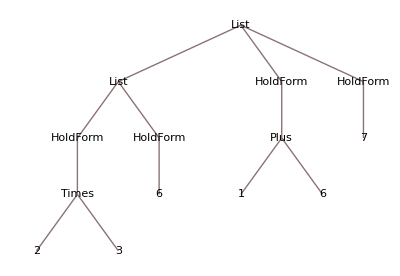

```mathematica
TreeForm[%]
```

```mathematica
HoldForm[Evaluate[1+1]]
```

2

```mathematica
Attributes[#]&/@{Hold, HoldForm, HoldComplete}
```

{{HoldAll,Protected},{HoldAll,Protected},{HoldAllComplete,Protected}}

```mathematica
HoldComplete[Evaluate[1+1],Sequence[a,b]]
```

HoldComplete[Evaluate[1+1],Sequence[a,b]]

```mathematica
ClearAll[f,g]
Hold[f]^:="what";
Hold[g]^:="the heck?";
f=g;
```

```mathematica
Hold[f]
```

what

```mathematica
Hold[Evaluate[f]]
```

the heck?

```mathematica
UpValues[f]
```

{HoldPattern[Hold[f]]:>what}

注意刚阐明的这种情况不会出现在HoldComplete上，因为HoldComplete不会搜索上值集。但是，如果在HoldComplete上定义了下值集（先去除保护），下值集会被应用。